# CalcPauliTransferEval

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

## Doc

```mathematica
?CalcPauliTransferEval
```

## Correctness

## Maps

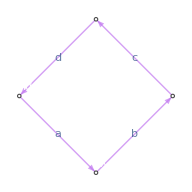

```mathematica
map = Subscript[PTMap, 0][0->{{1,a}},1->{{2,b}}, 2->{{3,c}}, 3->{{0,d}}];
DrawPauliTransferMap[map]
```

```mathematica
CalcPauliTransferEval[Subscript[X, 0], map];
Column @ MapAt[GetPauliString,%, {All,All,1}]
```

{{X_0,1,{{0,1}}}}
{{Y_0,2,{{1,b}}}}

```mathematica
CalcPauliTransferEval[Subscript[X, 0], {map,map,map}];
Column @ MapAt[GetPauliString,%, {All,All,1}]
```

{{X_0,1,{{0,1}}}}
{{Y_0,2,{{1,b}}}}
{{Z_0,3,{{2,c}}}}
{{Id_0,4,{{3,d}}}}

```mathematica
CalcPauliTransferEval[Subscript[X, 5], {map,map,map,map,map,map}];
Column @ MapAt[GetPauliString,%, {All,All,1}]
```

{{X_5,1,{{0,1}}}}
{{X_0 X_5,2,{{1,a}}}}
{{X_5 Y_0,3,{{2,b}}}}
{{X_5 Z_0,4,{{3,c}}}}
{{X_5,5,{{4,d}}}}
{{X_0 X_5,6,{{5,a}}}}
{{X_5 Y_0,7,{{6,b}}}}

## Circuits

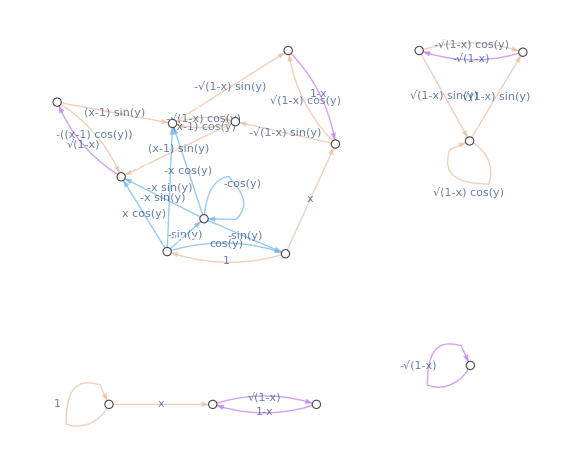

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[H, 1] Subscript[Damp, 0][x] Subscript[Rx, 1][y] ];
DrawPauliTransferMap[circ]
```

```mathematica
CalcPauliTransferEval[ Subscript[Y, 0] Subscript[Y, 1], circ]
GetPauliString /@ %[[-1,All,1]]
```

{{{{2,2},1,{{0,1}}}},{{{2,2},2,{{1,-1}}}},{{{2,2},3,{{2,-1}}}},{{{2,2},4,{{3,√(1-x)}}}},{{{2,2},5,{{4,Cos[y]}}},{{3,2},6,{{4,Sin[y]}}}}}

{Y_0 Y_1,Y_0 Z_1}

```mathematica
CalcPauliTransferEval[ Subscript[Y, 1], circ];
GetPauliString /@ %[[-1,All,1]]

ApplyPauliTransferMap[Subscript[Y, 1],circ]
```

{Y_1,Z_1,Y_1 Z_0,Z_0 Z_1}

-Cos[y] Y_1-x Cos[y] Y_1 Z_0-Sin[y] Z_1-x Sin[y] Z_0 Z_1

```mathematica
repeated = Join @@ Table[circ,10];

CalcPauliTransferEval[ Subscript[Y, 1], repeated];
Plus @@ GetPauliString /@ %[[-1,All,1]]

(ApplyPauliTransferMap[Subscript[Y, 1],repeated] /. {x->.1,y->.15})[[All,2;;]]
```

X_1+X_0 X_1+Y_1+X_0 Y_1+X_1 Z_0+Y_1 Z_0+Z_1+X_0 Z_1+Z_0 Z_1

X_1+X_0 X_1+Y_1+X_0 Y_1+X_1 Z_0+Y_1 Z_0+Z_1+X_0 Z_1+Z_0 Z_1

## Options

### OutputForm -> “Detailed”

```mathematica
circ = GetKnownCircuit["QFT", 3];
data = CalcPauliTransferEval[Subscript[X, 0], circ, "OutputForm"->"Detailed"];
```

```mathematica
Column @ Keys @ data
```

Ids
Layers
NumQubits
NumNodes
NumLeaves
States
Parents
Children
ParentFactors
Weights
Indegree
Outdegree
Coefficients
Strings

```mathematica
data["Ids"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

```mathematica
data["Layers"]
```

{{1},{2},{3},{4,5,6,7},{8,9,10,11},{12,13,14,15,16,17,18,19},{28,29,30,31,32,33,34,35},{36,37,38,39,40,41,42,43}}

```mathematica
data["States"]
```

<|1→X_0,2→X_0,3→X_0,4→X_0,5→X_0 Z_2,6→Y_0,7→Y_0 Z_2,8→X_0,9→X_0 Z_2,10→Y_0,11→Y_0 Z_2,12→X_0,13→X_0 Z_1,14→Y_0,15→Y_0 Z_1,16→X_0 Z_2,17→X_0 Z_1 Z_2,18→Y_0 Z_2,19→Y_0 Z_1 Z_2,28→Z_0,29→Z_0 Z_1,30→Y_0,31→Y_0 Z_1,32→Z_0 Z_2,33→Z_0 Z_1 Z_2,34→Y_0 Z_2,35→Y_0 Z_1 Z_2,36→Z_2,37→Z_1 Z_2,38→Y_2,39→Y_2 Z_1,40→Z_0 Z_2,41→Z_0 Z_1 Z_2,42→Y_2 Z_0,43→Y_2 Z_0 Z_1|>

```mathematica
data["Parents"]
```

<|1→{},2→{1},3→{2},4→{3},5→{3},6→{3},7→{3},8→{4},9→{5},10→{6},11→{7},12→{8,10},13→{8,10},14→{8,10},15→{8,10},16→{9,11},17→{9,11},18→{9,11},19→{9,11},28→{12},29→{13},30→{14},31→{15},32→{16},33→{17},34→{18},35→{19},36→{28},37→{29},38→{30},39→{31},40→{32},41→{33},42→{34},43→{35}|>

```mathematica
data["Children"]
```

<|1→{2},2→{3},3→{4,5,6,7},4→{8},5→{9},6→{10},7→{11},8→{12,13,14,15},9→{16,17,18,19},10→{12,13,14,15},11→{16,17,18,19},12→{28},13→{29},14→{30},15→{31},16→{32},17→{33},18→{34},19→{35},28→{36},29→{37},30→{38},31→{39},32→{40},33→{41},34→{42},35→{43},36→{},37→{},38→{},39→{},40→{},41→{},42→{},43→{}|>

```mathematica
data["Weights"]
```

<|1→1,2→1,3→1,4→1,5→2,6→1,7→2,8→1,9→2,10→1,11→2,12→1,13→2,14→1,15→2,16→2,17→3,18→2,19→3,28→1,29→2,30→1,31→2,32→2,33→3,34→2,35→3,36→1,37→2,38→1,39→2,40→2,41→3,42→2,43→3|>

```mathematica
data["Indegree"]
data["Outdegree"]
```

<|1→0,2→1,3→1,4→1,5→1,6→1,7→1,8→1,9→1,10→1,11→1,12→2,13→2,14→2,15→2,16→2,17→2,18→2,19→2,28→1,29→1,30→1,31→1,32→1,33→1,34→1,35→1,36→1,37→1,38→1,39→1,40→1,41→1,42→1,43→1|>

<|1→1,2→1,3→4,4→1,5→1,6→1,7→1,8→4,9→4,10→4,11→4,12→1,13→1,14→1,15→1,16→1,17→1,18→1,19→1,28→1,29→1,30→1,31→1,32→1,33→1,34→1,35→1,36→0,37→0,38→0,39→0,40→0,41→0,42→0,43→0|>

```mathematica
data["Coefficients"]
```

<|1→1,2→1,3→1,4→Cos[π/8]^2,5→Sin[π/8]^2,6→1/(2 √2),7→-1/(2 √2),8→Cos[π/8]^2,9→Sin[π/8]^2,10→1/(2 √2),11→-1/(2 √2),12→-1/(4 √2)+1/2 Cos[π/8]^2,13→1/(4 √2)+1/2 Cos[π/8]^2,14→1/(4 √2)+1/2 Cos[π/8]^2,15→1/(4 √2)-1/2 Cos[π/8]^2,16→1/(4 √2)+1/2 Sin[π/8]^2,17→-1/(4 √2)+1/2 Sin[π/8]^2,18→-1/(4 √2)+1/2 Sin[π/8]^2,19→-1/(4 √2)-1/2 Sin[π/8]^2,28→-1/(4 √2)+1/2 Cos[π/8]^2,29→1/(4 √2)+1/2 Cos[π/8]^2,30→-1/(4 √2)-1/2 Cos[π/8]^2,31→-1/(4 √2)+1/2 Cos[π/8]^2,32→1/(4 √2)+1/2 Sin[π/8]^2,33→-1/(4 √2)+1/2 Sin[π/8]^2,34→1/(4 √2)-1/2 Sin[π/8]^2,35→1/(4 √2)+1/2 Sin[π/8]^2,36→-1/(4 √2)+1/2 Cos[π/8]^2,37→1/(4 √2)+1/2 Cos[π/8]^2,38→-1/(4 √2)-1/2 Cos[π/8]^2,39→-1/(4 √2)+1/2 Cos[π/8]^2,40→1/(4 √2)+1/2 Sin[π/8]^2,41→-1/(4 √2)+1/2 Sin[π/8]^2,42→1/(4 √2)-1/2 Sin[π/8]^2,43→1/(4 √2)+1/2 Sin[π/8]^2|>

```mathematica
Column @ Normal @ data["Strings"]
```

X_0
X_0
X_0
Cos[π/8]^2 X_0+Y_0/(2 √2)+Sin[π/8]^2 X_0 Z_2-(Y_0 Z_2)/(2 √2)
Cos[π/8]^2 X_0+Y_0/(2 √2)+Sin[π/8]^2 X_0 Z_2-(Y_0 Z_2)/(2 √2)
(-1/(4 √2)+1/2 Cos[π/8]^2) X_0+(1/(4 √2)+1/2 Cos[π/8]^2) Y_0+(1/(4 √2)+1/2 Cos[π/8]^2) X_0 Z_1+(1/(4 √2)-1/2 Cos[π/8]^2) Y_0 Z_1+(1/(4 √2)+1/2 Sin[π/8]^2) X_0 Z_2+(-1/(4 √2)+1/2 Sin[π/8]^2) Y_0 Z_2+(-1/(4 √2)+1/2 Sin[π/8]^2) X_0 Z_1 Z_2+(-1/(4 √2)-1/2 Sin[π/8]^2) Y_0 Z_1 Z_2
(-1/(4 √2)-1/2 Cos[π/8]^2) Y_0+(-1/(4 √2)+1/2 Cos[π/8]^2) Z_0+(-1/(4 √2)+1/2 Cos[π/8]^2) Y_0 Z_1+(1/(4 √2)+1/2 Cos[π/8]^2) Z_0 Z_1+(1/(4 √2)-1/2 Sin[π/8]^2) Y_0 Z_2+(1/(4 √2)+1/2 Sin[π/8]^2) Z_0 Z_2+(1/(4 √2)+1/2 Sin[π/8]^2) Y_0 Z_1 Z_2+(-1/(4 √2)+1/2 Sin[π/8]^2) Z_0 Z_1 Z_2
(-1/(4 √2)-1/2 Cos[π/8]^2) Y_2+(1/(4 √2)-1/2 Sin[π/8]^2) Y_2 Z_0+(-1/(4 √2)+1/2 Cos[π/8]^2) Y_2 Z_1+(1/(4 √2)+1/2 Sin[π/8]^2) Y_2 Z_0 Z_1+(-1/(4 √2)+1/2 Cos[π/8]^2) Z_2+(1/(4 √2)+1/2 Sin[π/8]^2) Z_0 Z_2+(1/(4 √2)+1/2 Cos[π/8]^2) Z_1 Z_2+(-1/(4 √2)+1/2 Sin[π/8]^2) Z_0 Z_1 Z_2

```mathematica
SimplifyPaulis @ Last @ data @ "Strings"
```

-1/4 (1+√2) Y_2+1/4 (-1+√2) Y_2 Z_0+(Y_2 Z_1)/4+1/4 Y_2 Z_0 Z_1+Z_2/4+(Z_0 Z_2)/4+1/4 (1+√2) Z_1 Z_2-1/4 (-1+√2) Z_0 Z_1 Z_2

```mathematica
% // N
```

-0.603553 Y_2+0.103553 Y_2 Z_0+0.25 Y_2 Z_1+0.25 Y_2 Z_0 Z_1+0.25 Z_2+0.25 Z_0 Z_2+0.603553 Z_1 Z_2-0.103553 Z_0 Z_1 Z_2

```mathematica
data["NumQubits"]
data["NumNodes"]
data["NumLeaves"]
```

3

35

8

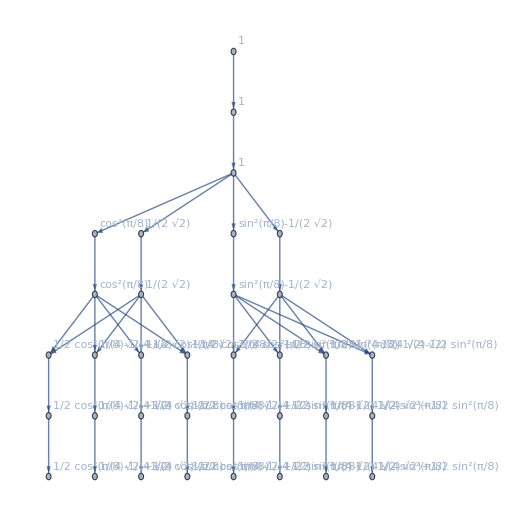

```mathematica
Graph[
	Thread /@ Normal @ data @ "Children" // Flatten,
	VertexLabels-> Normal @ data @  "Coefficients"
]
```

### CombineStates

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[H, 1] Subscript[Damp, 0][x] Subscript[Rx, 1][y] ];
circ = Join @@ Table[circ,5];

CalcPauliTransferEval[ Subscript[Y, 1], circ][[-1,All,1]]
Length[%]

CalcPauliTransferEval[ Subscript[Y, 1], circ, "CombineStrings"->False][[-1,All,1]]
Length[%]
```

{{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1}}

9

{{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1},{2,0},{3,0},{2,3},{3,3},{2,1},{3,1},{2,3},{3,3},{1,3},{2,3},{3,3},{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1},{2,3},{3,3},{1,3},{2,1},{3,1},{1,1},{2,1},{3,1},{2,1},{3,1},{1,1},{2,0},{3,0},{2,3},{3,3},{1,0},{1,3},{2,1},{3,1},{1,1},{2,0},{3,0},{2,3},{3,3},{2,1},{3,1},{2,3},{3,3},{1,3},{2,3},{3,3},{2,1},{3,1},{1,1},{2,1},{3,1},{2,3},{3,3},{1,3},{2,3},{3,3},{2,3},{3,3},{1,3},{2,3},{3,3},{1,3},{2,3},{3,3}}

78

```mathematica
history = CalcPauliTransferEval[ Subscript[Y, 1], circ];
ancestors = Flatten[history, 1][[All,3]];
Length /@ ancestors //Max

history = CalcPauliTransferEval[ Subscript[Y, 1], circ, "CombineStrings"->False];
ancestors =Flatten[history, 1][[All,3]];
Length /@ ancestors //Max
```

2

1

### CacheMaps

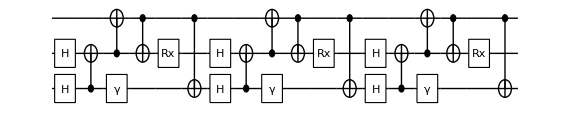

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[H, 1] Subscript[C, 0][Subscript[X, 1]] Subscript[C, 1][Subscript[X, 2]]Subscript[Damp, 0][x] Subscript[C, 2][Subscript[X, 1]] Subscript[Rx, 1][y]Subscript[C, 2][Subscript[X, 0]] ];
circ = Join @@ Table[circ,3];
DrawCircuit[circ]
```

```mathematica
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"Never"]
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"UntilCallEnd"]
```

0.093662

0.018925

```mathematica
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"Forever"]
First @ Timing @ CalcPauliTransferEval[ Subscript[Y, 1], circ, "CacheMaps"->"Forever"]
```

0.021346

0.007441

### AssertValidChannels

```mathematica
CalcPauliTransferEval[Subscript[Y, 2] Subscript[Y, 1] Subscript[Z, 0],Subscript[Damp, 0][x]]
CalcPauliTransferEval[Subscript[Y, 2] Subscript[Y, 1] Subscript[Z, 0],Subscript[Damp, 0][x], AssertValidChannels->False]
```

{{{{2,2,3},1,{{0,1}}}},{{{2,2,3},2,{{1,1-x}}}}}

{{{{2,2,3},1,{{0,1}}}},{{{2,2,0},2,{{1,1/2 (1-√(1-x) Conjugate[√(1-x)]-√x Conjugate[√x])}}},{{2,2,3},3,{{1,1/2 (1+√(1-x) Conjugate[√(1-x)]-√x Conjugate[√x])}}}}}

## Errors

```mathematica
CalcPauliTransferEval[Subscript[Id, 1],Subscript[PTMap, 2][{eh}]]
```

CalcPauliTransferEval::error: Could not pre-compute the Pauli transfer maps due to the below error:

CalcPauliTransferMatrix::error: Circuit contained an unrecognised or unsupported gate: PTMap_0[{eh}]

$Failed

```mathematica
CalcPauliTransferEval[Subscript[Id, 1],Subscript[Bop, 0]]
```

CalcPauliTransferEval::error: Could not pre-compute the Pauli transfer maps due to the below error:

CalcPauliTransferMatrix::error: Circuit contained an unrecognised or unsupported gate: Bop_0

$Failed

```mathematica
CalcPauliTransferEval[Subscript[Id, -1],Subscript[H, 0]]
```

CalcPauliTransferEval::error: Invalid arguments. See ?CalcPauliTransferEval

$Failed

```mathematica
CalcPauliTransferEval[1,Subscript[H, 0]]
```

CalcPauliTransferEval::error: Invalid arguments. See ?CalcPauliTransferEval

$Failed

```mathematica
CalcPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "CacheMaps"->"x"]
```

CalcPauliTransferEval::error: Option "CacheMaps" must be one of "Forever", "UntilCallEnd" or "Never".

$Failed

```mathematica
CalcPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "CombineStrings"->"x"]
```

CalcPauliTransferEval::error: Option "CombineStrings" must be True or False. See ?CalcPauliTransferEval.

$Failed

```mathematica
CalcPauliTransferEval[Subscript[X, 0],Subscript[X, 0], "BadOption"->False]
```

OptionValue::nodef: Unknown option BadOption for {ApplyPauliTransferMap,CalcPauliTransferMap}.

$Failed

```mathematica
CalcPauliTransferEval[]
```

CalcPauliTransferEval::error: Invalid arguments. See ?CalcPauliTransferEval

$Failed